CSE 577*Advanced Geometric Modeling
Instructor:Dianne Hansford
Student:Yu-Hsuan, Chuang
Student ID:1211219305
Homework 1:A link between Bezier and Lagrange curve schemes
Due 31 January 2017 by midnight

Blend of De Castelfau and Aitken algorithm

^□Equation:
b(r, i, t) = T(r, i, alpha)*b(r-1, i, t) + (1-T(r, i, alpha))*b(r-1, i+1, t);
	where T(r, i, alpha) = [(1-alpha)*t[i+r] + alpha - t ]/[(1-alpha)*(t[i+r]-t[i]) + alpha];


Implement code
(If there is something wrong at the manipulate part when opening this file,please evaluate again the following cell)

```mathematica
(* data points *)
d1 ={{0,0},{1,0},{0,2}};
d2 ={{0,0,0},{0,1,0},{0.5,1,0},{2,0,0}};
d3 ={{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}};

e1 = {1,0};
p = Table[{0,0},{i,1,8}];
Do[
t = i/7.0;
theta = ((1-t)*(-36) + t*216)*(Pi/180);
mat = {{Cos[theta], -Sin[theta]},{Sin[theta], Cos[theta]}};
p[[i+1]] = mat.e1,
{i,0,7,1}];(* figure4 data points *)


(* Blend of De Castelfau and Aitken algorithm *)
blend[b_,r_,i_,tt_, aalpha_]:=(
(* if r=0, return b0, else, return the computation result of the red equation above *)
If [r==0,x=b[[i+1]],x=(((1-aalpha)*ti[[i+r+1]]+aalpha-tt)/((1-aalpha)*(ti[[i+r+1]]-ti[[i+1]])+aalpha))*blend[b,r-1,i,tt,aalpha]+(1-(((1-aalpha)*ti[[i+r+1]]+aalpha-tt)/((1-aalpha)*(ti[[i+r+1]]-ti[[i+1]])+aalpha)))*blend[b,r-1,i+1,tt,aalpha]];
Return [x];
);

(* Load dataset points *)
b= d3;
n=Length[b]-1;
dimension=Length[b[[1]]];
ti = Table[i/n,{i, 0, n}]; (* initial ti-value with i/n *)
getcolor = RandomColor[10];
aalpha = 0.5; (* set alpha-value equal to 0.5 *)
tx = 0.3; (* set t-value equal to 0.3 *)

(* Show the construction polygons and vertices for one alpha-value and t-value pair *)
Print["alpha = ",aalpha, ", t = ",tx];
Print["dimension = ", dimension];
Print["b = ",MatrixForm[b], "  ", b];

(* compute the polygon points of each map stage *)
polyr[r_] :=Table[blend[b,r,i,tx,aalpha],{i,0,n-r}];

If[dimension==3,
(* compute the 3D curve *)
curve= ParametricPlot3D[blend[b,n,0,t,aalpha], {t, 0, 1}];(* line up the initial 3D data points B0 *)
poly=Graphics3D[{Thick,Green,Line[b]}];(* show the initial 3D data points B0 *)
points=Graphics3D[{Green,PointSize[Large],Point[b]}];(* line up each stage 3D points Br *)
nested=Table[Graphics3D[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];(* show each stage 3D points Br *)
curvept=Graphics3D[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha]]}];
,
(* compute the 2D curve *)
curve= ParametricPlot[blend[b,n,0,t,aalpha], {t, 0, 1}];(* line up the initial 2D data points B0 *)
poly=Graphics[{Thick,Green,Line[b]}];(* show the initial 2D data points B0 *)
points=Graphics[{Green,PointSize[Large],Point[b]}];(* line up each stage 2D points Br *)
nested=Table[Graphics[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];(* show each stage 2D points Br *)
curvept=Graphics[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha]]}];
];
Show[{curvept,nested,points,poly,curve}]

(* manipulate t-value, alpha-value and dataset(use popupmenu), the following method is same as above *)
Manipulate[
b=Switch[dataset,1,d1, 2, d2, 3, d3, figure4, p];
n=Length[b]-1;
tx = t;
aalpha = alpha;
dimension=Length[b[[1]]];
ti = Table[i/n,{i, 0, n}];
If[dimension==3,
curve= ParametricPlot3D[blend[b,n,0,txx,aalpha], {txx, 0, 1}];
poly=Graphics3D[{Thick,Green,Line[b]}];
points=Graphics3D[{Green,PointSize[Large],Point[b]}];
nested=Table[Graphics3D[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics3D[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha]]}];
,
curve= ParametricPlot[blend[b,n,0,txx,aalpha], {txx, 0, 1}];poly=Graphics[{Thick,Green,Line[b]}];
points=Graphics[{Green,PointSize[Large],Point[b]}];
nested=Table[Graphics[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha]]}];
];
Show[{curvept,nested,points,poly,curve}]
,{{t,0.5},0,1},{{alpha,1},-2,2},{{dataset,1},{1,2,3,figure4},PopupMenu}
]
```

alpha = 0.5, t = 0.3

dimension = 3

b = (0 | 0 | 0
1 | 0 | 0
1 | 0 | 1
1 | 1 | 1
1 | 1 | 0
0 | 1 | 0)  {{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}}

-Graphics3D-

Discussion
-- What does this program do?
The main goal of this program is to implement the blend of De Casteljau algorithm and Aitken algorithm in the paper “Link between Bezier and Lagrange curve and surface schemes” by G. Farin and P. Barry. By this program, I have learned how the author blends the two algorithms and how it work each map stage, and also help me get the hang of Mathematica. 

-- How did you determine your code is correct?
To verify my code, I adjust the alpha value to see whether the results match the properties of the blending algorithm. When alpha equals to 0, the result of the blending algorithm should be same as the result of Aitken algorithm; On the other hand, when alpha equals to 1, the result of the blending algorithm should be same as the result of Casteljau algorithm. The following code is the implementation of De Casteljau and Aitken. The first result is Casteljau algorithm which is same as the result of the blending algorithm when alpha equals to 1. The second result is Aitken algorithm which is same as the blending algorithm when alpha equals to 0. We can compare the results using the manipulate part above.

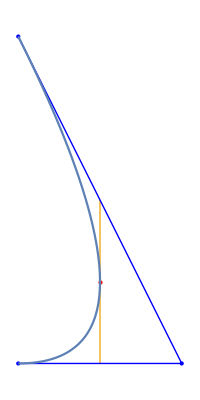

De Casteljau algorithm

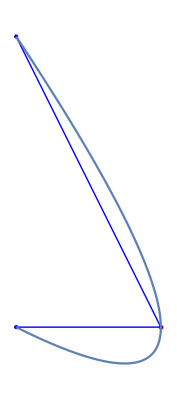

Aitken algorithm

```mathematica
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];
aa[b_, r_, i_, t_] :=(
If [r==0,x=b[[i+1]],x=((ti[[i+r+1]]-t)/(ti[[i+r+1]]-ti[[i+1]]))*aa[b,r-1,i,t]+(1-((ti[[i+r+1]]-t)/(ti[[i+r+1]]-ti[[i+1]])))*aa[b,r-1,i+1,t]];
Return [x];
);
d1 ={{0,0},{1,0},{0,2}};
b= d1;
n=Length[b]-1;
dimension=Length[b[[1]]];
ti = Table[i/n,{i, 0, n}]; 
getcolor = RandomColor[10];
tx = 0.5; 

polyr[r_] :=Table[dca[b,r,i,tx],{i,0,n-r}];

If[dimension==3,
curve= ParametricPlot3D[dca[b,n,0,t], {t, 0, 1}]; 
poly=Graphics3D[{Thick,Blue,Line[b]}];
points=Graphics3D[{Blue,PointSize[Large],Point[b]}];
nested=Table[Graphics3D[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics3D[{PointSize[Large],Red,Point[dca[b,n,0,tx]]}];
,
curve= ParametricPlot[dca[b,n,0,t], {t, 0, 1}];
poly=Graphics[{Thick,Blue,Line[b]}];
points=Graphics[{Blue,PointSize[Large],Point[b]}];
nested=Table[Graphics[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics[{PointSize[Large],Red,Point[dca[b,n,0,tx]]}];
];
Show[{curvept,nested,points,poly,curve}]
Print["De Casteljau algorithm"];
polyr[r_] :=Table[aa[b,r,i,tx],{i,0,n-r}];
If[dimension==3,
curve= ParametricPlot3D[aa[b,n,0,t], {t, 0, 1}]; 
poly=Graphics3D[{Thick,Blue,Line[b]}];
points=Graphics3D[{Blue,PointSize[Large],Point[b]}];
nested=Table[Graphics3D[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics3D[{PointSize[Large],Red,Point[aa[b,n,0,tx]]}];
,
curve= ParametricPlot[aa[b,n,0,t], {t, 0, 1}];
poly=Graphics[{Thick,Blue,Line[b]}];
points=Graphics[{Blue,PointSize[Large],Point[b]}];
nested=Table[Graphics[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics[{PointSize[Large],Red,Point[aa[b,n,0,tx]]}];
];
Show[{curvept,nested,points,poly,curve}]
Print["Aitken algorithm"];
```

-- Why did you select these data sets?
I select data sets that include 2D and 3D because I want to see how this method works in different dimensions. In addition, data sets with a different number of data points(different n-value) could help me observe each map stage more clearly. By selecting the different dimension and a different number of data points helps me understand thoroughly how this method works and know how to select data points for a specific curve implement in the future.

-- Any other comments or observations?
In the paper, Goldman has suggested replacing alpha-value by two independent parameters alpha-value and beta-value. The following is the implementation of this possible generalization.

```mathematica
d3 ={{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}};

blend[b_,r_,i_,tt_, aalpha_, bbeta_]:=(
If [r==0,x=b[[i+1]],x=(((1-bbeta)*ti[[i+r+1]]+bbeta-tt)/((((1-bbeta)*ti[[i+r+1]])-((1-aalpha)*ti[[i+1]]))+bbeta))*blend[b,r-1,i,tt,aalpha, bbeta]+(1-(((1-bbeta)*ti[[i+r+1]]+bbeta-tt)/((((1-bbeta)*ti[[i+r+1]])-((1-aalpha)*ti[[i+1]]))+bbeta)))*blend[b,r-1,i+1,tt,aalpha]];
Return [x];
);

b= d3;
n=Length[b]-1;
dimension=Length[b[[1]]];
ti = Table[i/n,{i, 0, n}]; 
getcolor = RandomColor[10];
aalpha = 0.8; 
bbeta = 1.2;
tx = 0.3;

Print["alpha = ",aalpha,", beta = ",bbeta,", t = ",tx];
Print["dimension = ", dimension];
Print["b = ",MatrixForm[b], "  ", b];

polyr[r_] :=Table[blend[b,r,i,tx,aalpha,bbeta],{i,0,n-r}];

If[dimension==3,
curve= ParametricPlot3D[blend[b,n,0,t,aalpha,bbeta], {t, 0, 1}]; 
poly=Graphics3D[{Thick,Green,Line[b]}];
points=Graphics3D[{Green,PointSize[Large],Point[b]}];
nested=Table[Graphics3D[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics3D[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha,bbeta]]}];
,
curve= ParametricPlot[blend[b,n,0,t,aalpha,bbeta], {t, 0, 1}];
poly=Graphics[{Thick,Green,Line[b]}];
points=Graphics[{Green,PointSize[Large],Point[b]}];
nested=Table[Graphics[{Thick,getcolor[[r]],Line[polyr[r]]}],{r,1,n}];
curvept=Graphics[{PointSize[Large],Red,Point[blend[b,n,0,tx,aalpha,bbeta]]}];
];
Show[{curvept,nested,points,poly,curve}]
```

alpha = 0.8, beta = 1.2, t = 0.3

dimension = 3

b = (0 | 0 | 0
1 | 0 | 0
1 | 0 | 1
1 | 1 | 1
1 | 1 | 0
0 | 1 | 0)  {{0,0,0},{1,0,0},{1,0,1},{1,1,1},{1,1,0},{0,1,0}}

-Graphics3D-

Therefore, the new interval is [ (1-alpha)*t[i], (1-beta)*t[i+r]+beta ] and the changes of the curve will have different effects at each endpoint.